```mathematica
arrivalRateData=Import["D:\\School\\CS1538-Project\\data\\RAW-DATA.xlsx", {"Data",3,Range[4,63],11}];
DistributionFitTest[arrivalRateData, PoissonDistribution[3.5],"TestConclusion"]
```

The null hypothesis that the data is distributed according to the PoissonDistribution[3.5] is not rejected at the 5 percent level based on the Pearson χ^2 test.

```mathematica
queueServiceTime=Import["D:\\School\\CS1538-Project\\data\\RAW-DATA.xlsx",{"Data",2,Range[2,61],2}];
H =DistributionFitTest[queueServiceTime, NormalDistribution[97.78,79.80],"HypothesisTestData"];
```

```mathematica
H["TestDataTable",All]
```

| Statistic | P-Value
Anderson-Darling | -60. | 1.
Cramér-von Mises | 20. | 2.88658×10^-15
Jarque-Bera ALM | 354.043 | 0.
Mardia Combined | 354.043 | 0.
Mardia Kurtosis | 14.7337 | 3.91841×10^-49
Mardia Skewness | 63.5856 | 1.53549×10^-15
Pearson χ^2 | 60. | 3.6243×10^-9
Shapiro-Wilk | 0.782794 | 5.15611×10^-8

```mathematica
R=RandomVariate[d=NormalDistribution[97.78,79.80],60];
g=DistributionFitTest[R,d,"HypothesisTestData"];
```

```mathematica
g["TestDataTable",All]
```

| Statistic | P-Value
Anderson-Darling | 2.76182 | 0.0364021
Cramér-von Mises | 0.492205 | 0.0416925
Jarque-Bera ALM | 5.68622 | 0.0663812
Kolmogorov-Smirnov | 0.141755 | 0.162766
Kuiper | 0.152086 | 0.329985
Mardia Combined | 5.68622 | 0.0663812
Mardia Kurtosis | 1.86809 | 0.0617498
Mardia Skewness | 0.401549 | 0.526291
Pearson χ^2 | 11.5 | 0.319911
Shapiro-Wilk | 0.975636 | 0.272413
Watson U^2 | 0.0833559 | 0.386761

```mathematica
Mean[queueServiceTime]
```

97.7833

```mathematica
StandardDeviation[queueServiceTime]
```

79.7998

```mathematica
test=DistributionFitTest[queueServiceTime,NormalDistribution[97.7833,79.7998],"HypothesisTestData"]
```

HypothesisTestData[…]

```mathematica
test["TestConclusion"]
```

0.121098[TestConclusion]

```mathematica
cashierServiceTime=Import["D:\\School\\CS1538-Project\\data\\RAW-DATA.xlsx",{"Data",2,Range[2,61],3}];
```

```mathematica
m=Mean[cashierServiceTime];
std=StandardDeviation[cashierServiceTime];
test = DistributionFitTest[cashierServiceTime,NormalDistribution[m,std],"HypothesisTestData"]
```

HypothesisTestData[…]

```mathematica
test["TestDataTable","KolmogorovSmirnov"]
```

DistributionFitTest::ties: Ties exist in the data and will be ignored for the {"KolmogorovSmirnov"} test, which assumes unique values.

| Statistic | P-Value
Kolmogorov-Smirnov | 0.205821 | 0.0104746

```mathematica
KolmogorovSmirnovTest[cashierServiceTime,NormalDistribution[m,std],"ShortTestConclusion"]
```

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the {"KolmogorovSmirnov"} test, which assumes unique values.

Reject

```mathematica
DistributionFitTest[cashierServiceTime,ExponentialDistribution[1./15.35],"HypothesisTestData"]
```

HypothesisTestData[…]

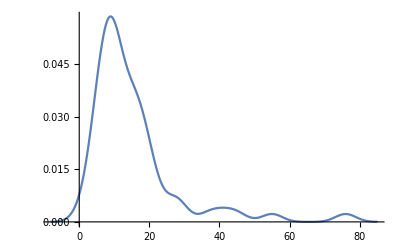

```mathematica
Show[SmoothHistogram[cashierServiceTime]]
```

```mathematica
StandardDeviation[cashierServiceTime]
```

12.9652

```mathematica
Mean[cashierServiceTime]
```

15.35

```mathematica
updatedCST=Import["D:\\School\\CS1538-Project\\data\\RAW-DATA.xlsx",{"Data",5,Range[1,53],1}];
```

```mathematica
DistributionFitTest[updatedCST,UniformDistribution[{2,28}],"HypothesisTestData"]
```

HypothesisTestData[…]

```mathematica
Mean[updatedCST]
```

12.0189

```mathematica
StandardDeviation[updatedCST]
```

5.68565

```mathematica
DistributionFitTest[updatedCST,NormalDistribution[12.018867924528301,5.685645102556139],"HypothesisTestData"]
```

HypothesisTestData[…]

```mathematica
normalCheckOut=Import["D:\\School\\CS1538-Project\\NormalCheckOut.txt","Data"];
```